```mathematica
importedDat=Import["/Users/eblu/Documents/Undergrad/Fall 2022/CDS DS 210/ds210-graph-project/graph-project/src/data/facebook_combined.txt","Table"]
```

```mathematica
graph=Graph[(#/.List->UndirectedEdge)&/@importedDat]
```

```mathematica
GraphPlot[graph,EdgeLabels->None,VertexLabels->None,ImageSize->Large,GraphLayout->"SpringElectricalEmbedding",PlotTheme->"Scientific"]
```

-Graphics-

```mathematica
minicut=FindGraphPartition[graph];
```

```mathematica
HighlightGraph[graph,Map[Subgraph[graph,#]&, minicut]]
```

$Aborted

```mathematica
Solve[(-ω^2 r^2)/2+ϵ r^4/2==ℰ,r]
```

{{r→-(√(ω^2/ϵ-(√(8 ℰ ϵ+ω^4))/ϵ))/(√2)},{r→(√(ω^2/ϵ-(√(8 ℰ ϵ+ω^4))/ϵ))/(√2)},{r→-(√(ω^2/ϵ+(√(8 ℰ ϵ+ω^4))/ϵ))/(√2)},{r→(√(ω^2/ϵ+(√(8 ℰ ϵ+ω^4))/ϵ))/(√2)}}

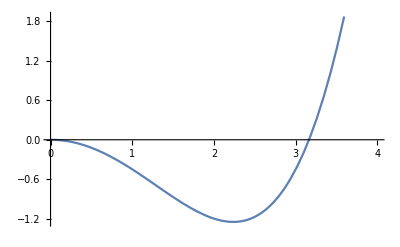

```mathematica
Plot[-r^2/2+0.1 r^4/2,{r,0,4}]
```